# Markov chain Monte Carlo demonstration/documentation

## Load in MCMC routine

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"mcmc.m"}]];
```

## Calling the routine

#### Syntax

MCMCModelFit[data, errors, model, paramspec, ivars, numsteps, options]

#### Inputs

1. data must be given as:
{{ivar1, dvar1}, {ivar2, dvar2}, ..., {ivarN, dvarN}}
where ivar is the independent variable, dvar is the dependent variable, and N is the number of data points. Either the ivars or dvars can be vector valued; if the independent variable is a vector, then we're just dealing with a function of multiple variables, and if the dependent variable is, then we have a vector field.

2. errors must have the same length as data (= N), with each entry giving the errors in the corresponding dependent variable supplied in data. If each dvar is just a number, then so too should be each element of errors; if instead each dvar is a vector, then each element of errors should also be a vector of the same length.

3. model should evaluate to either a number or a numerical vector (depending on dvar) when all parameters and independent variables are set.

4. paramspec either gives the results of a previous MCMC run (w/ same model, data, etc.--just to add on more iterations), or lists the model parameters like so:
{{param1, ival1, spread1, domain1}, ...}
a) Each param should be symbolic.
b) ival is the initial parameter value.
c) spread is roughly how far to try to change the parameter each step in the Markov chain. In this routine we select new parameters values based on an exponential distribution of the form Exp[Δparam/spread]. My Numerical Recipes book advises setting these spreads so that the average candidate acceptance is 10-40%.
d) Each domain is either Reals or a list of all possible values the parameter can take on (needs to be a uniform grid).

5. ivars gives a list of symbolic independent variables, in the same order as in data, on which model depends. If there's only one, then it need not be a list.

6. numsteps is the number of Markov chain steps to perform.

#### Options

```mathematica
Options[MCMCModelFit]
```

{BurnFraction→0.1,Debug→False,ProgressMonitor→Step/MaxSteps  MCMC`Private`TimeProgress[TimeElapsed,DoneFraction]
CurrentParameters,ProgressInterval→10,SaveTo→None,SaveInterval→1000,Compiled→False}

"ProgressMonitor" can use any combination of the strings "CurrentParameters", "TimeElapsed", "DoneFraction", "Step", "MaxSteps", and "AverageAcceptance", which will be replaced appropriately. “AverageAcceptance” should only be used if individual model evaluations are quite time consuming.

## Example/test: straight line

#### Generate fake data with fake errors, then run MCMC routine

```mathematica
error=2;
dattab=Table[{x,5.x-3.+RandomVariate[NormalDistribution[0,error]]},{x,0,3,.01}];
errors=Table[error,{x,0,3,.01}];
Timing[mcmc=MCMCModelFit[dattab,errors,(a x+b),{{a,3,.1,Real},{b,-1,.1,Real}},{x},100000,"Compiled"->True]]
```

{10.8927,MCMCResult[{a→5.16357,b→-3.12066},«100000»]}

#### Available data from MCMC

```mathematica
mcmc["Properties"]
```

{BestFitParameters,ParameterErrors,AverageAcceptance,TimeSpent,NumSteps,Parameters,ProposalSpreads,ParameterDomains,BurnFraction,BurnEnd,BestFitPlot,BestFitReducedChisq,CorrelationMatrix,ParameterRun,ParametersLogPRun,TransitionLogPRun,ParameterRunPlots,ParameterHistograms}

#### Results

{BestFitParameters→{a→5.16357,b→-3.12066},ParameterErrors→{a→0.131348,b→0.228284},AverageAcceptance→0.463263,CorrelationMatrix→(1. | -0.86449
-0.86449 | 1.)}

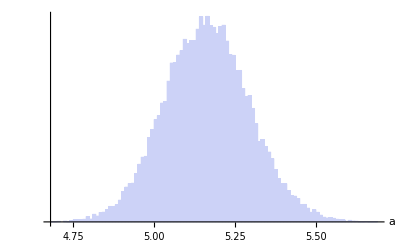
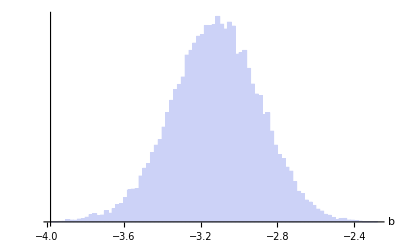

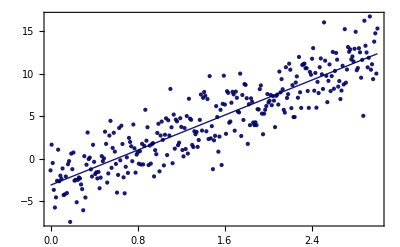

```mathematica
FilterRules[mcmc[[1]],{"BestFitParameters","ParameterErrors","AverageAcceptance","CorrelationMatrix"}]
mcmc["ParameterHistograms"]
mcmc["BestFitPlot"]
```

#### Comparison with analytics

In this case of a straight line we can also compare with analytic results. The best-fit parameters and parameter errors obtained with MCMC vs. analytic least-squares methods agree nicely! (See e.g. Bevington 2003, ch. 6.)

```mathematica
Delta=Total[1/errors^2]Total[dattab[[All,1]]^2/errors^2]-Total[dattab[[All,1]]/errors^2]^2;

Join[{"TrueParameters"->{a->5,b->-3},"MCMCBestFitParameters"->mcmc["BestFitParameters"],"AnalyticBestFitParameters"->{a->(Total[1/errors^2]Total[(Times@@@dattab)/errors^2]-Total[dattab[[All,1]]/errors^2]Total[dattab[[All,2]]/errors^2])/Delta,b->(Total[dattab[[All,1]]^2/errors^2]Total[dattab[[All,2]]/errors^2]-Total[dattab[[All,1]]/errors^2]Total[(Times@@@dattab)/errors^2])/Delta},
"MCMCErrors"->mcmc["ParameterErrors"],"AnalyticErrors"->
{a->Sqrt[1/Delta*Total[1/errors^2]],b->Sqrt[1/Delta*Total[dattab[[All,1]]^2/errors^2]]}},FilterRules[mcmc[[1]],{"BestFitReducedChisq","AverageAcceptance","CorrelationMatrix"}]]
```

{TrueParameters→{a→5,b→-3},MCMCBestFitParameters→{a→5.16357,b→-3.12066},AnalyticBestFitParameters→{a→5.16447,b→-3.1206},MCMCErrors→{a→0.131348,b→0.228284},AnalyticErrors→{a→0.13267,b→0.229983},AverageAcceptance→0.463263,BestFitReducedChisq→1.26221,CorrelationMatrix→(1. | -0.86449
-0.86449 | 1.)}

#### Verify error estimates reproduce expected normal distribution

Here we perform MCMC fitting 500 times, each time recording the alleged parameter errors from MCMC as well as from analytics (see above). We then determine what percentage of the time the true parameters fall within the error estimates, which should be 68% (since they are both 1-σ). Works!

```mathematica
Monitor[trtab=Table[
error=2;
dattab=Table[{x,5.x-3.+RandomVariate[NormalDistribution[0,error]]},{x,0,3,.01}];
errors=Table[error,{x,0,3,.01}];
res=MCMCModelFit[dattab,errors,(a x+b),{{a,5,.02,Real},{b,-3,.02,Real}},{x},10000,"Compiled"->True];
Delta=Total[1/errors^2]Total[dattab[[All,1]]^2/errors^2]-Total[dattab[[All,1]]/errors^2]^2;
{(a/.res["BestFitParameters"]),(a/.res["ParameterErrors"]),Sqrt[1/Delta*Total[1/errors^2]]}
,
{ii,500}
];,
ii//N]
res=(({Abs[#[[1]]-5]<#[[2]],Abs[#[[1]]-5]<#[[3]]}&/@trtab/.True->1/.False->0//Total)/500//N);
{"MCMCResult"->res[[1]],"AnalyticResult"->res[[2]]}
```

{0.666,0.666}

Both should be (?):

```mathematica
1-(1-(CDF[NormalDistribution[0,1],x]/.x->1.))2
```

0.682689

## Example: curvy line

#### Generate fake data with fake errors, then run MCMC routine

Important to give good initial guesses for parameters. Try messing up the guesses below, and you may sit at a local minimum.

```mathematica
error=1.5;
dattab=Table[{x,1.3x-2Sin[2x]+7+RandomVariate[NormalDistribution[0,error]]},{x,0,10,.1}];
errors=Table[error,{x,0,10,.1}];
spr=.04;
mcmc=MCMCModelFit[dattab,errors,a x+b Sin[c x]+d,{{a,1.3,spr,Real},{b,-2,spr,Real},{c,2,spr,Real},{d,7,spr,Real}},{x},100000]
FilterRules[mcmc[[1]],{"AverageAcceptance"}]
```

MCMCResult[{a→1.41159,b→-2.1008,c→2.00521,d→6.57209},«100000»]

{AverageAcceptance→0.263047}

#### Results

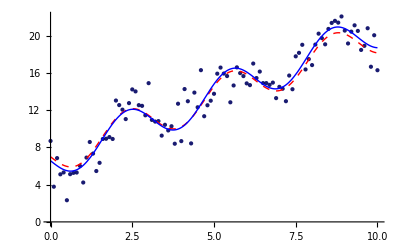

{BestFitParameters→{a→1.41159,b→-2.1008,c→2.00521,d→6.57209},ParameterErrors→{a→0.0495894,b→0.213088,c→0.0180113,d→0.275897},AverageAcceptance→0.263047,CorrelationMatrix→(1. | 0.105815 | 0.21085 | -0.847401
0.105815 | 1. | 0.046061 | -0.109415
0.21085 | 0.046061 | 1. | -0.118975
-0.847401 | -0.109415 | -0.118975 | 1.)}

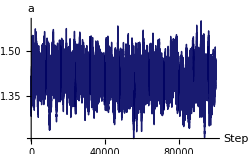
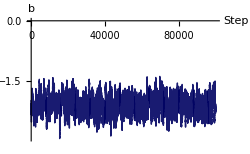
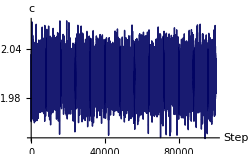
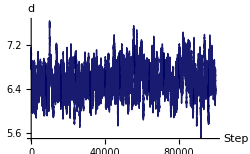

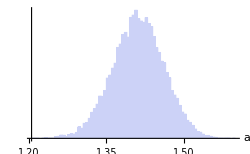
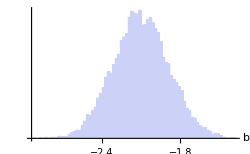
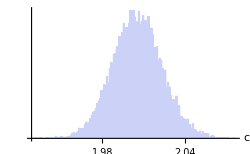
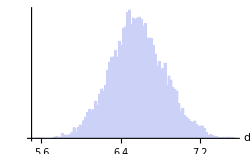

```mathematica
Show[ListPlot[dattab,Joined->False],Plot[{7+1.3x-2Sin[2x],a x+b Sin[c x]+d/.mcmc["BestFitParameters"]},{x,0,10},PlotStyle->{Directive[Red,Dashed,Opacity[1]],Blue}]]
FilterRules[mcmc[[1]],{"BestFitParameters","ParameterErrors","AverageAcceptance","CorrelationMatrix"}]
mcmc["ParameterRunPlots",ImageSize->250]
mcmc["ParameterHistograms",ImageSize->250]
```

## Real-world[ish] example: fitting radial velocity data from an eccentric stellar binary

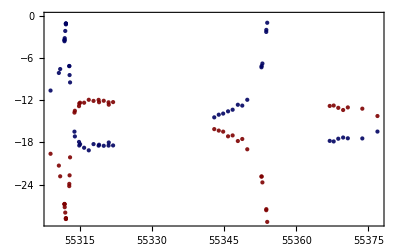

```mathematica
rvdata={{55308.9298,-10.58,-19.61},{55310.6587,-8.07,-21.3},{55310.9353,-7.51,-22.83},{55311.8277,-3.54,-26.81},{55311.8353,-3.38,-26.77},{55311.8427,-3.33,-26.82},{55311.8775,-3.1,-27.24},{55311.9883,-2.07,-28.01},{55312.1251,-1.02,-28.79},{55312.1265,-1.03,-28.93},{55312.1278,-1.13,-28.9},{55312.1292,-0.99,-28.85},{55312.8216,-7.07,-24.23},{55312.83,-7.1,-23.91},{55312.8899,-8.37,-22.69},{55312.9897,-9.42,-20.12},{55313.9043,-16.45,-13.73},{55313.9888,-17.13,-13.47},{55314.8513,-17.92,-12.81},{55314.9021,-18.43,-12.43},{55315.0767,-18.24,-12.32},{55315.913,-18.75,-12.32},{55316.8788,-19.12,-11.9},{55317.87,-18.23,-12.06},{55318.9274,-18.45,-11.91},{55319.0179,-18.32,-12.25},{55319.9909,-18.47,-12.04},{55320.9937,-18.44,-12.26},{55321.0389,-18.,-12.6},{55321.9376,-18.42,-12.23},{55342.9718,-14.41,-16.09},{55343.9095,-14.03,-16.3},{55344.8253,-13.87,-16.45},{55345.8418,-13.55,-17.12},{55346.7917,-13.32,-16.99},{55347.8754,-12.61,-17.79},{55348.7957,-12.73,-17.5},{55349.836,-11.9,-18.97},{55352.7859,-7.26,-22.86},{55352.8244,-7.07,-22.86},{55352.985,-6.72,-23.7},{55353.779,-2.21,-27.67},{55353.7974,-1.92,-27.52},{55353.9845,-0.9,-29.34},{55366.9826,-17.77,-12.78},{55367.8032,-17.85,-12.72},{55368.7601,-17.46,-13.05},{55369.7711,-17.29,-13.36},{55370.7447,-17.4,-12.99},{55373.759,-17.42,-13.17},{55376.9083,-16.44,-14.22}};

ListPlot[{rvdata[[All,1;;2]],rvdata[[All,{1,3}]]},Joined->False]
```

```mathematica
GetTrueAnomaly[e_?NumericQ]/;(0≤e<1):=Module[{int},int=Interpolation[Reverse/@Join[{{-Pi,-Pi}},Table[{f,Re[2 ArcTan[((1-e) Tan[f/2])/Sqrt[1-e^2]]-(e Sin[f] Sqrt[1-e^2])/(1+e Cos[f])]},{f,-Pi+2Pi/1000.,Pi-2Pi/1000,2 Pi/1000.}],{{Pi,Pi}}]];
(Evaluate[int][Mod[#+Pi,2Pi]-Pi]+Round[#/2/Pi]*2 Pi)&];
GetTrueAnomaly[espec_List]:=Module[{func},Interpolation[Flatten[Table[func=GetTrueAnomaly[e];
Table[{e,ν,func[ν]},{ν,-Pi,Pi,2 Pi/1000.}],{e,espec[[1]],espec[[2]],espec[[3]]}],1]]];

Ω=Convert[2Pi/41.8/Day,Hertz]/Hertz;
fint=GetTrueAnomaly[{.7,.93,.001}];
Clear[ffunc];
ffunc[e_,ν_]:=If[.7<e<.93,fint[e,ν],70];

rvmodelcomp=Compile[{K,e,phorad,Tp,V,Per,t},((K(e Sin[phorad]+Sin[phorad-ffunc[e,Mod[(t-Tp)/Per*2Pi+Pi,2Pi]-Pi]])+V))];
rvmodel[K_?NumericQ,e_?NumericQ,phorad_?NumericQ,Tp_?NumericQ,V_?NumericQ,Per_?NumericQ,t_?NumericQ]:=rvmodelcomp[K,e,phorad,Tp,V,Per,t];

Sp[x__List]/;(Equal@@Length/@{x})&&Length[{x}]>1:=Transpose[{x}];
```

MCMCResult[{K1→9.14946,q→1.03515,e→0.830421,pho→50.5373,Tp→55312.6,V→-15.2604,Porb→41.8209},«100000»]

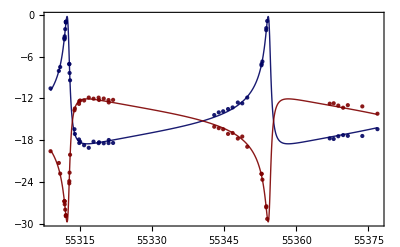

{BestFitParameters→{K1→9.14946,q→1.03515,e→0.830421,pho→50.5373,Tp→55312.6,V→-15.2604,Porb→41.8209},ParameterErrors→{K1→0.161712,q→0.016231,e→0.0050644,pho→0.809299,Tp→0.0121793,V→0.057877,Porb→0.0333},TimeSpent→239.04377 Second,CorrelationMatrix→(1. | 0.431196 | 0.794835 | -0.0624322 | 0.306241 | -0.192093 | 0.0472804
0.431196 | 1. | 0.0154734 | 0.0138872 | -0.0263735 | -0.517445 | -0.00774383
0.794835 | 0.0154734 | 1. | -0.0434854 | 0.395617 | 0.0255201 | -0.186166
-0.0624322 | 0.0138872 | -0.0434854 | 1. | -0.625383 | -0.0465578 | 0.1254
0.306241 | -0.0263735 | 0.395617 | -0.625383 | 1. | 0.0175979 | -0.281234
-0.192093 | -0.517445 | 0.0255201 | -0.0465578 | 0.0175979 | 1. | 0.00373718
0.0472804 | -0.00774383 | -0.186166 | 0.1254 | -0.281234 | 0.00373718 | 1.),AverageAcceptance→0.121316,BestFitReducedChisq→0.822803}

```mathematica
s=.2;
rvmcmc=MCMCModelFit[{#[[1]],{#[[2]],#[[3]]}}&/@rvdata,{#[[2]],#[[3]]}&/@rvdata/._?NumericQ->.5,{rvmodel[K1,e,pho Pi/180.,Tp,V,Porb,t],rvmodel[K1/q,e,pho Pi/180+Pi,Tp,V,Porb,t]},{{K1,9.35,0.5 s,Real},{q,1.06,.05 s,Real},{e,.834,.02 s,Real},{pho,49.5,3s,Real},{Tp,55312,.05 s,Real},{V,-15,.2 s,Real},{Porb,41.8051,.1s,Real}},{t},10^5,"ProgressInterval"->10]

rvmcmc["BestFitPlot"]
rvmcmc[{"BestFitParameters","ParameterErrors","TimeSpent","CorrelationMatrix","AverageAcceptance","BestFitReducedChisq"}]
```

## Discrete-valued parameters

#### Check it out. All parameters (except discrete one) strongly correlated.

{BestFitParameters→{a→4.59512,b→1.2907,c→-1.97013,n→1.},ParameterErrors→{a→0.19881,b→0.0210639,c→0.328314,n→0.},AverageAcceptance→0.172809,CorrelationMatrix→(1. | -0.942859 | -0.920916 | -0.0217171
-0.942859 | 1. | 0.856422 | -0.0361224
-0.920916 | 0.856422 | 1. | 0.00811055
-0.0217171 | -0.0361224 | 0.00811055 | 1.)}

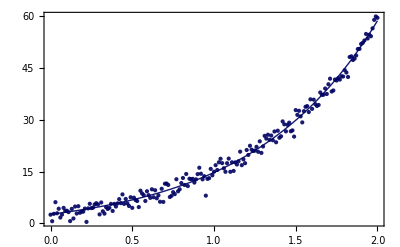

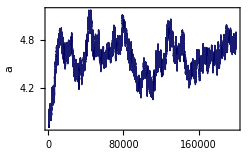
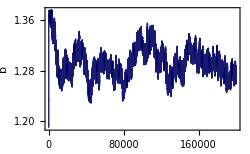
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

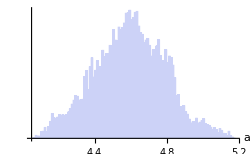
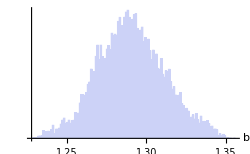
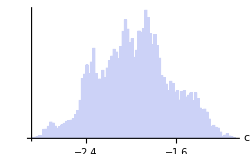
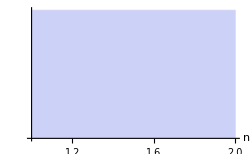

```mathematica
error=1.5;
dattab=Table[{x,4.5 Exp[1.3 x]-2+RandomVariate[NormalDistribution[0,error]]},{x,0,2,.01}];
errors=Table[error,{x,0,2,.01}];
spr=.01;
mcmc=MCMCModelFit[dattab,errors,If[n==1,a Exp[b x]+c,a Sin[b x]+c],{{a,3,spr,Real},{b,1,spr,Real},{c,-1,spr,Real},{n,2,2,{1,2}}},{x},2*^5,"Compiled"->True];
FilterRules[mcmc[[1]],{"BestFitParameters","ParameterErrors","AverageAcceptance","CorrelationMatrix"}]
mcmc["BestFitPlot"]
mcmc["ParameterRunPlots",ImageSize->250]
mcmc["ParameterHistograms",ImageSize->250]
```